{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.61224×10^-7,7.05306×10^-6,0.0000326531,0.0000896,0.000190433,0.00034769,0.00057391,0.000881633,0.0012834,0.00179174,0.0024192,0.00317832,0.00408163,0.00514168,0.006371,0.00778214,0.00938762,0.0112,0.0132318,0.0154956,0.0180039,0.0207692,0.0238041,0.0271211,0.0307328,0.0346517,0.0388903,0.0434612,0.0483769,0.05365,0.059293,0.0653184,0.0717388,0.0785667,0.0858146,0.0934951,0.101621,0.110204,0.119258,0.128794,0.138825,0.149365,0.160424,0.172017,0.184155,0.196851,0.210118,0.223967,0.238413,0.253466,0.26914,0.285447,0.3024,0.320011,0.338293,0.357259,0.37692,0.39729,0.418381,0.440205,0.462775,0.486104,0.510204,0.505595,0.499909,0.493116,0.485184,0.476082,0.465778,0.454241,0.441439,0.427342,0.411918,0.395136,0.376964,0.357371,0.336325,0.313796,0.289752,0.264161,0.236992,0.208214,0.177796,0.145706,0.111912,0.0763847,0.0390909}

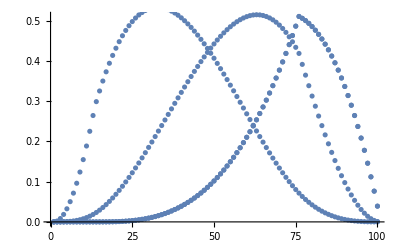

```mathematica
a=ReadList["~/cppsandbox/tmp2.dat",Real]
aa=ListPlot[a];
bb=ListPlot[b];
cc=ListPlot[c];
dd=ListPlot[d];
Show[aa,bb,cc,dd]
```

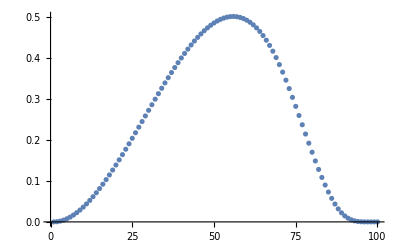

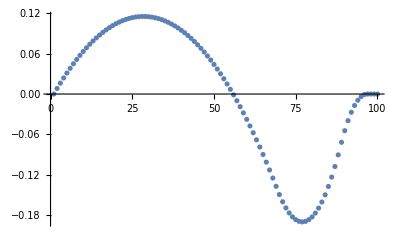

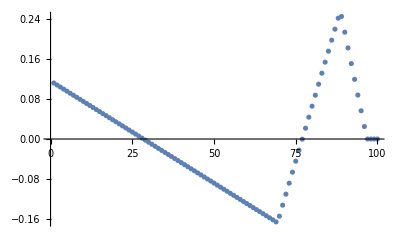

```mathematica
a=Import["~/phd-stuff/courses/comp_phys/B(2,4).csv"];
aa=Table[a[[i]][[1]],{i,1,100}];
bb=Normalize[Table[a[[i]][[2]],{i,1,100}]];
cc=Normalize[Table[a[[i]][[3]],{i,1,100}]];
ListPlot[aa,PlotRange->All]
ListPlot[bb,PlotRange->All]
ListPlot[cc,PlotRange->All]
```

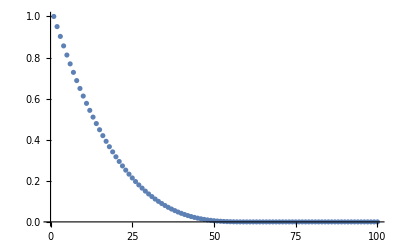

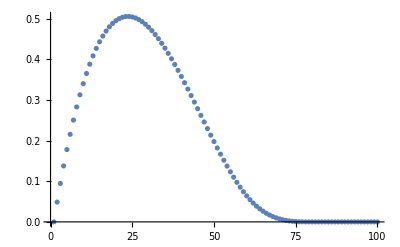

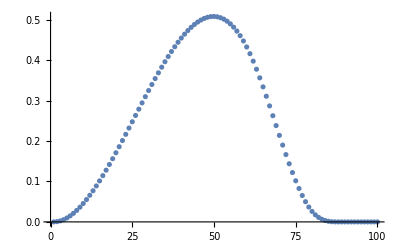

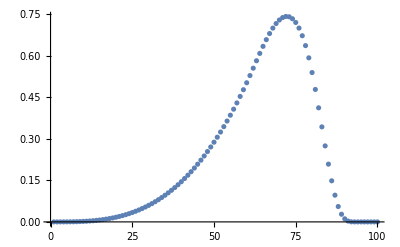

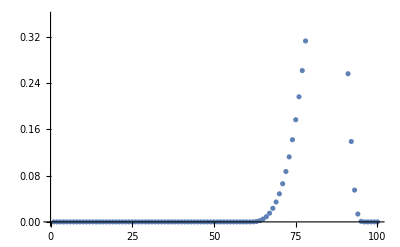

```mathematica
a1=Import["~/phd-stuff/courses/comp_phys/B(0,4).csv"];
a2=Import["~/phd-stuff/courses/comp_phys/B(1,4).csv"];
a3=Import["~/phd-stuff/courses/comp_phys/B(2,4).csv"];
a4=Import["~/phd-stuff/courses/comp_phys/B(3,4).csv"];
a5=Import["~/phd-stuff/courses/comp_phys/B(4,4).csv"];
b1=Table[a1[[i]][[1]],{i,1,100}];
b2=Table[a2[[i]][[1]],{i,1,100}];
b3=Table[a3[[i]][[1]],{i,1,100}];
b4=Table[a4[[i]][[1]],{i,1,100}];
b5=Table[a5[[i]][[1]],{i,1,100}];
ListPlot[b1]
ListPlot[b2]
ListPlot[b3]
ListPlot[b4]
ListPlot[b5]
```